### check section “UAV-Manipulator” in companion pdf

## Import vector field and transformed vector field

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"uav_manipulator_transformation.nb"}]];
```

### define a useful function to test some equalities

```mathematica
test[t_,x_,V_,W_,X_]:=Module[
{xx},
D[V[Subscript[xx, 1],Array[Subscript[xx, #]&,Length[x],2]],{Array[Subscript[xx, #]&,Length[x]+1]}].Join[{1},X[t,x]]-
W[t,x]/.Thread[Array[Subscript[xx, #]&,Length[x]+1]-> Join[{t},x]]
]
```

## Get control for thrust propelled system and unit vector second order system

### defined some useful variables (these are just dummy names)

```mathematica
y1={p1,p2,p3,v1,v2,v3,n1,n2,n3,Ω1,Ω2,Ω3};
y2={r1,r2,r3,ω1,ω2,ω3};
y=Join[y1,y2];

yRandom=f[xRandom[]]/.PhysicalConstants;
y1Random=yRandom[[1;;12]];
y2Random=yRandom[[13;;18]];
```

## Subsystem 1: thrust propelled system

### Controller for thrust propelled system

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"controllers_for_transformed_systems/controller_thrust_propelled_system.m"}]]
(*gains of torque cascaded controller*)
BoundedDoubleIntegratorGains={kp-> 1.5,kv-> √2 √1.5,σp-> 0.6,σv-> 0.6,β-> 0.1};
AttitudeControllerGains={kp-> 3,kd-> √2 √3,kVp-> 100,kVd-> 200,β-> 0.1};

z3={0,0,0};
gravity[t_]=pd''[t]+g e3/.PhysicalConstants;
ControllerSubsystem1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,n1_,n2_,n3_,Ω1_,Ω2_,Ω3_}]=
ThrustPropelledController[
t,y1,gravity,
BoundedDoubleIntegratorGains,
(*{"PD" ,AttitudeControllerGains,{"Precise"},Null}*)
{"BackStepping",AttitudeControllerGains,{"Precise"},"on"}
];

v1cl[t_,y1_]:=ControllerSubsystem1[t,y1][[1]]
V1[t_,y1_]:=ControllerSubsystem1[t,y1][[2]]
W1[t_,y1_]:=ControllerSubsystem1[t,y1][[3]]
X1[t_,y1_]:=ControllerSubsystem1[t,y1][[4]]

Timing[v1cl[0.1,y1Random]]
Timing[Chop[test[0.1,y1Random,V1,W1,X1]]]
```

{0.088,{5.12019,{1.22031,-2.93178,-1.53319}}}

{0.592,0}

## Subsystem 1: unit vector second order system

### Controller for unit vector second order system

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"controllers_for_transformed_systems/cascaded_attitude_control.m"}]];
(*gains of torque cascaded controller*)
AttitudeControllerGains={kp-> 1.5,kd-> 1.73,kVp-> 10,kVd-> 20,β-> 0.1};


ControllerSubsystem2[t_,{r1_,r2_,r3_,ω1_,ω2_,ω3_}]=TorqueBacksteppingController[
t,Null,y2,
{nd,Null,Null,Null,Null,Null,Null},
{Null,Null,Null},
{Null,Null,Null,Null,Null},
AttitudeControllerGains,
"Precise",
Null,
"on"
];

v2cl[t_,y2_]:=ControllerSubsystem2[t,y2][[2]][[1]];
V2[t_,y2_]:=ControllerSubsystem2[t,y2][[2]][[2]];
W2[t_,y2_]:=ControllerSubsystem2[t,y2][[2]][[3]];
X2[t_,y2_]:=ControllerSubsystem2[t,y2][[2]][[4]];

Timing[v2cl[0.1,y2Random]]
Timing[Chop[test[0.1,y2Random,V2,W2,X2]]]
```

{0.008,{-0.332817,-0.840481,-0.0549462}}

{0.04,0}

## yaw control law

```mathematica
τψcl[t_,{p1_,p2_,p3_,r11_,r12_,r13_,r21_,r22_,r23_,r31_,r32_,r33_,P1_,P2_,P3_,R11_,R12_,R13_,R21_,R22_,R23_,R31_,R32_,R33_,v1_,v2_,v3_,ω1_,ω2_,ω3_,V1_,V2_,V3_,Ω1_,Ω2_,Ω3_}]=-Ω3;
```

## complete control law in transformed coordinates

```mathematica
vcl[t_,y_]:=
Join[
Flatten[v1cl[t,y[[1;;12]]]],
v2cl[t,y[[13;;18]]]
]
```

## complete control law in original coordinates

```mathematica
Ucl[t_,x_]:=
ucl[
x,
vcl[t,Evaluate[(f[x]-Join[pd[t],pd'[t],ConstantArray[0,12]])/.PhysicalConstants]],
τψcl[t,x]
]/.PhysicalConstants

Timing[Ucl[0.1,xRandom[]]]
```

{0.12,{14.2785,0.278694,-1.41422,-0.109948,0.546528,-1.19498}}

## closed loop vector field

```mathematica
Xcl[t_,x_]:=X[x,Ucl[t,x]]
VV[t_,x_]:=(V1[t,#[[1;;12]]]+V2[t,#[[13;;18]]])&[f[x]-Join[pd[t],pd'[t],ConstantArray[0,12]]]
WW[t_,x_]:=(W1[t,#[[1;;12]]]+W2[t,#[[13;;18]]])&[f[x]-Join[pd[t],pd'[t],ConstantArray[0,12]]]

(*Xcl[t_,x_]:=X[x,Ucl[t,x]]
VV[t_,x_]:=(V1[t,#[[1;;12]]])&[f[x]-Join[pd[t],pd'[t],ConstantArray[0,12]]]
WW[t_,x_]:=(W1[t,#[[1;;12]]])&[f[x]-Join[pd[t],pd'[t],ConstantArray[0,12]]]*)
Timing[Chop[test[0.1,xRandom[]/.PhysicalConstants,VV,WW,Xcl]/.PhysicalConstants]]
```

{3.976,0}

## Projection: take any element in R36 and project it into X

```mathematica
projR1[U_,V_]:=U.ConjugateTranspose[V]
projR2[SVD_]:=projR1[SVD[[1]],SVD[[3]]]
projR3[R_]:=projR2[Evaluate[SingularValueDecomposition[R]]]

Proj[{p1_,p2_,p3_,r11_,r12_,r13_,r21_,r22_,r23_,r31_,r32_,r33_,P1_,P2_,P3_,R11_,R12_,R13_,R21_,R22_,R23_,R31_,R32_,R33_,v1_,v2_,v3_,ω1_,ω2_,ω3_,V1_,V2_,V3_,Ω1_,Ω2_,Ω3_}]:=
Join[
{p1,p2,p3},
Flatten[projR3[ {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}]],
{p1,p2,p3}+l {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}.e3,
Flatten[projR3[ {{R11,R12,R13},{R21,R22,R23},{R31,R32,R33}}]],
{v1,v2,v3},
{ω1,ω2,ω3},
{v1,v2,v3}+l  {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}.Skew[{ω1,ω2,ω3}].e3,
{Ω1,Ω2,Ω3}
]/.PhysicalConstants;
error[x_]:=Proj[x]-x
Chop[error[xRandom[]/.PhysicalConstants]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Simulation

```mathematica
stepsize=0.01;
NN=1000;

z3=ConstantArray[0,3];
x0=Join[z3,Flatten[IdentityMatrix[3]],l e3,Flatten[IdentityMatrix[3]],z3,z3,z3,z3]/.PhysicalConstants;
(*x0=xRandom[]/.PhysicalConstants;*)
stateList={};
stateListStar={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
(*xstar0 = h[yplusplusstar[time]]/.PhysicalConstants;*)
xstar0 = xplusplusstar[time]/.PhysicalConstants;
input =Ucl[time,x0];
tensions= Tensions[x0,input]/.PhysicalConstants;

stateList= Join[stateList,{x0}];
stateListStar= Join[stateListStar,{xstar0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

xd=  X[x0,input]/.PhysicalConstants;
x0=Proj[x0+stepsize xd]/.PhysicalConstants;

If[i≥200 kk,Beep[];Print[i];kk=kk+1];
]
```

200

400

600

800

1000

## saving data

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state.mat",stateList];
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state_star.mat",stateListStar];
```

### export

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state.mx",stateList];
Export[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state_star.mx",stateListStar];
Export[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_input.mx",inputList];
Export[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_tensions.mx",tensionsList];
```

### Import

```mathematica
(*stateList=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state.mx"];*)
(*stateListStar=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state_star.mx"];*)
(*inputList=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_input.mx"];*)
(*tensionsList=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_tensions.mx"];*)
```

### necessary for the plots that follow

```mathematica
NN=Length[stateList]
XTicksLabels={{1,0},{200,2},{400,4},{600,6},{800,8},{1000,10}};
xc[i_,comp_]:=stateList[[i,comp]]
uc[i_,comp_]:=inputList[[i,comp]]
```

1000

```mathematica
(*stateList=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state.mat"][[1]];
stateListStar=Import[NotebookDirectory[]<>"figures/uav_manipulator/plot_trajectory_matlab/data_state_star.mat"][[1]];*)
```

## Metric error

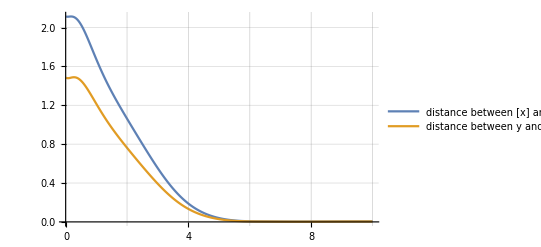
-Graphics-time (s)

```mathematica
errordY[i_]:=dY[f[stateList[[i,;;]]],f[stateListStar[[i,;;]]]]/.PhysicalConstants
errordX[i_]:=dXToStar[stepsize(i-1),stateList[[i,;;]]]/.PhysicalConstants

Labeled[
ListLinePlot[{
Table[errordX[i],{i,1,NN}],
Table[errordY[i],{i,1,NN}]
},
PlotLegends->Placed[{"distance between [x] and [x(]^*)_(++)","distance between y and (y^*)_(++)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)",""},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_error_distances.pdf",%];
```

## Error position

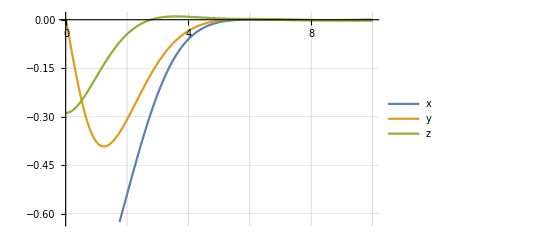
-Graphics-time (s)error(m)

```mathematica
errorp=(m stateList[[1;;NN,{1,2,3}]]+M stateList[[1;;NN,{13,14,15}]])/(m+M)-Table[(pd[stepsize(i-1)]),{i,1,NN}]/.PhysicalConstants;
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_error_position.pdf",%];
```

## Error velocity

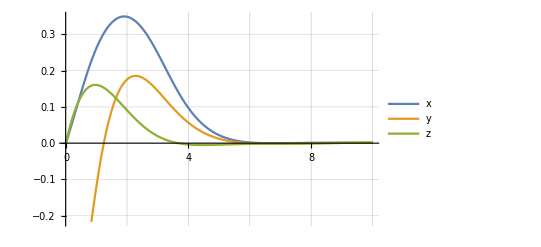
-Graphics-time (s)error(m)

```mathematica
errorv=(m stateList[[1;;NN,{25,26,27}]]+M stateList[[1;;NN,{31,32,33}]])/(m+M)-Table[(pd'[stepsize(i-1)]),{i,1,NN}]/.PhysicalConstants;
Labeled[
ListLinePlot[{
errorv[[;;,1]],
errorv[[;;,2]],
errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_error_velocity.pdf",%];
```

## “Neglected” angular velocities (not seen by equivalence class)

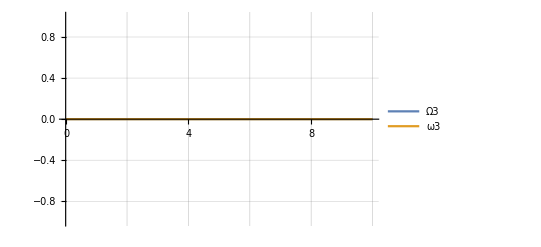
-Graphics-time (s)hz

```mathematica
Labeled[
ListLinePlot[{
Chop[stateList[[1;;NN,36]]],
Chop[stateList[[1;;NN,30]]]
},
PlotLegends->Placed[{"Ω3","ω3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","hz"},{Bottom,Left},RotateLabel->True
]
```

## Error attitude

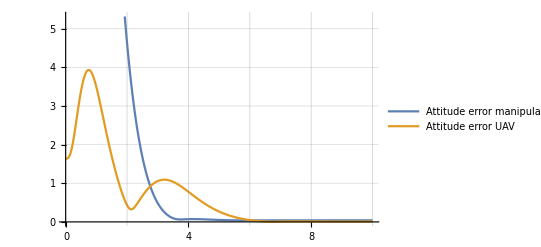
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[
ArcCos[xc[i,{6,9,12}].nd[stepsize(i-1)]] 180/π,
{i,1,NN}
],
Table[
ArcCos[xc[i,{18,21,24}].((pd''[stepsize(i-1)]+g e3)/Norm[pd''[stepsize(i-1)]+g e3])] 180/π/.PhysicalConstants,
{i,1,NN}
]
},
PlotLegends->Placed[{"Attitude error manipulator","Attitude error UAV"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_attitude_errors.pdf",%];
```

## UAV thrust

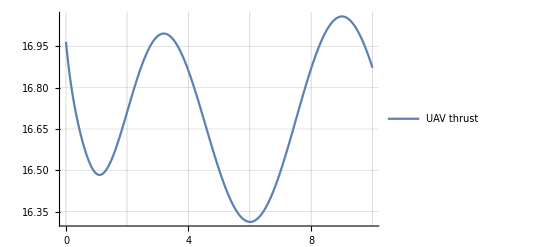
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1]
},
PlotLegends->Placed[{"UAV thrust"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_input_uav_thrust.pdf",%];
```

## UAV torque

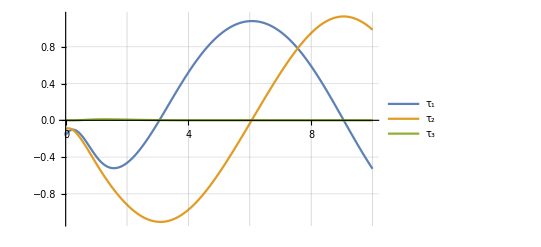
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[2],
aux[3],
aux[4]
},
PlotLegends->Placed[{"τ_1","τ_2","τ_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

## Manipulator torque

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_input_uav_torque.pdf",%];
```

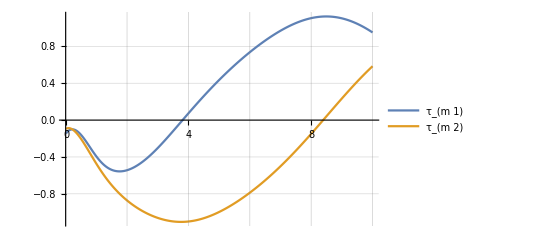
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[5],
aux[6]
},
PlotLegends->Placed[{"τ_(m 1)","τ_(m 2)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_input_manipulator_torque.pdf",%];
```

## UAV torque + manipulator torque

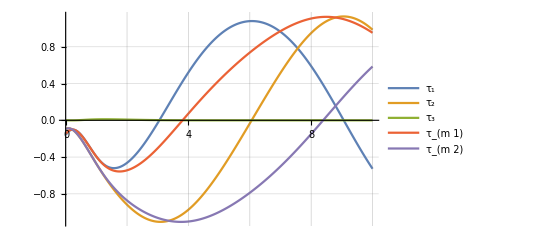
-Graphics-time (s)torque(N m)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[2],
aux[3],
aux[4],
aux[5],
aux[6]
},
PlotLegends->Placed[{"τ_1","τ_2","τ_3","τ_(m 1)","τ_(m 2)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","torque(N m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_input_torques.pdf",%];
```

## Tensions

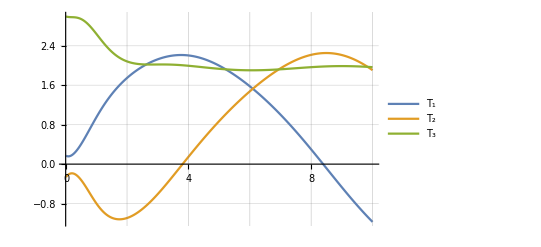
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2],
aux[3]
},
PlotLegends->Placed[{"T_1","T_2","T_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_tensions.pdf",%];
```

## Thrust and Tensions

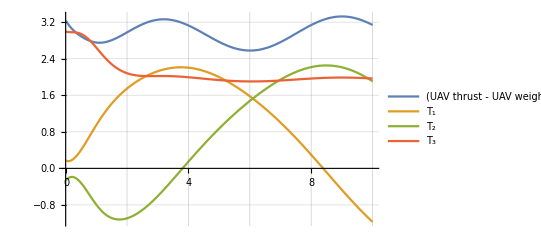
-Graphics-time (s)force(N)

```mathematica
aux1[comp_]:=inputList[[1;;NN,comp]]
aux2[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux1[1]-(M g/.PhysicalConstants),
aux2[1],
aux2[2],
aux2[3]
},
PlotLegends->Placed[{"(UAV thrust - UAV weight)","T_1","T_2","T_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_manipulator/sim_input_forces.pdf",%];
```